```mathematica
(* function *)
```

```mathematica
newton[f_, {x_,x0_}, ϵ_]:=
Module[{xnext, xprev = N[x0],g,n=1},
g[t_]:=f/.x->t;
xnext=xprev-g[xprev]/g'[xprev]//N;
While[Abs[xnext-xprev]≥ϵ && n≤100,
Print[Abs[xnext-xprev]];
xprev = xnext;
xnext=xprev-g[xprev]/g'[xprev]//N;
n++;];
{xnext,n}
];
```

```mathematica
f[x_]:=Sin[x]-0.1x
```

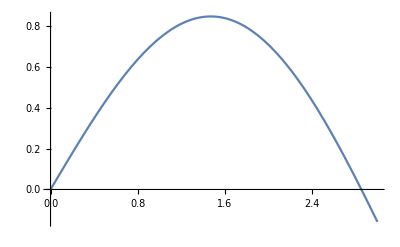

```mathematica
Plot[f[x], {x,0,3}]
```

```mathematica
newton[f[x],{x,3}, 10^-3]
```

0.145762

0.00189516

{2.85234,3}

```mathematica
FindRoot[f[x], {x,3}]
```

{x→2.85234}

```mathematica
ϕ[x_]:=x-f[x]/f'[x]
```

```mathematica
Reduce[{Abs[ϕ'[x]]<1,1<x<5},x, Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2.20087<x<3.8762

```mathematica
newton[f[x], {x,2.2},10^-3]
```

2.85234

```mathematica
newton[f[x], {x,2.0},10^-3]
```

2.85234

```mathematica
newton[f[x], {x,1.8},10^-3]
```

2.85234

```mathematica
(*доcтаточное, но не необходимое условие*)
```

```mathematica
T1 = Table[{i,newton[f[x], {x,i},10^-3][[2]]},{i,2.2,3.8,0.1}]
```

{{2.2,4},{2.3,4},{2.4,3},{2.5,3},{2.6,3},{2.7,3},{2.8,2},{2.9,2},{3.,3},{3.1,3},{3.2,3},{3.3,2},{3.4,3},{3.5,3},{3.6,3},{3.7,4},{3.8,4}}

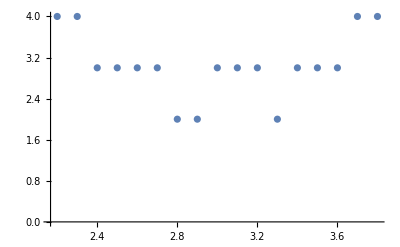

```mathematica
ListPlot[T1]
```

```mathematica
T2=Table[{i,newton[f[x], {x,2.2},10^-i][[2]]},{i,1,6,1}];
```

0.85475

-0.19954

0.85475

-0.19954

0.85475

-0.19954

-0.00286754

0.85475

-0.19954

-0.00286754

0.85475

-0.19954

-0.00286754

0.85475

-0.19954

-0.00286754

-1.10082×10^-6

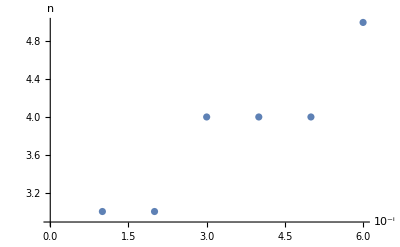

```mathematica
ListPlot[T2, AxesLabel->{10^-i, n}]
```

```mathematica
Task 2
```

```mathematica
FixedPoint[ϕ,3.]
```

2.85234

```mathematica
FixedPoint[#-f[#]/f'[#]&,3.]
```

2.85234

```mathematica
ψ[x_]:= FixedPoint[#-f[#]/f'[#]&,x]
```

```mathematica
ψ[3.]
```

2.85234

```mathematica
Clear[a]
```

```mathematica
a[n_]:=a[n]=Sqrt[2+a[n-1]]
```

```mathematica
a[0] =1
```

1

```mathematica
a[4]//N
```

1.99572

```mathematica
a[1000]//N
```

2.

```mathematica
Limit[a[n], n->∞]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -1021+n.

Hold[lim_(n→∞) a[n]]

```mathematica
g[x_]:=Sqrt[2+x];
```

```mathematica
Reduce[{(g[x]-g[y])/(x-y)<1,x>0,y>0}, {x,y}, Reals]
```

x>0&&(0<y<x||y>x)

```mathematica
FixedPoint[g,1.]
```

2.

```mathematica
Task 3
```

```mathematica
fa[list_]:=
Module[{sqr,summa, len},
sqr = list^2;
summa = Total[sqr];
len = Length[sqr];
summa/len
];
```

```mathematica
Clear[a]
```

```mathematica
a = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
fa[a]
```

11

```mathematica
fb[list_]:=
Module[{x=1},
While[list[[x]]≥0 && x≤Length[list],
x++;
];
x
]
```

```mathematica
Clear[b]
```

```mathematica
b = {1,2,-4,3,5}
```

{1,2,-4,3,5}

```mathematica
fb[b]
```

3

```mathematica
fc[list_]:=
Module[{maximum, index=1},
maximum=Max[list];
While[list[[index]]≠maximum ,
index++;
];
{maximum,index}
];
```

```mathematica
fc[b]
```

{5,5}

```mathematica
fd[l_List]:=
Module[{l1={},l2={},l3={},count=0,index=1, flags=False, a={}},
While[index ≤ Length[l],
If[l[[index]]<0,
If[flags==False,
flags=True,
If[Mod[count,2]==0,
l1=Join[l1,a],
l2 = Join[l2,a]];
];
a=Join[a,{l[[index]]}];
count++;
];
index++;
];
Join[l1,l2,l3]
];
```

```mathematica
fd[{1,-1,1,-2,2,3,-3,4}]
```

{-1,-2,-1}

```mathematica
f4[l_List]:=Module[{lcopy=l,sel,index,sel2},
sel=Select[l,#<0&];
index=Position[l,#]&/@sel//Flatten//DeleteDuplicates//Sort;
sel2=Take[l,{index[[#]]+1,index[[#+1]]-1}]&/@Range[1,Length[sel]-1];
lcopy=l[[1;;index[[1]]-1]];
AppendTo[lcopy,sel];
AppendTo[lcopy,l[[Last@index+1;;Length[l]]]];
If[EvenQ[Length[#]],PrependTo[lcopy,#],AppendTo[lcopy,#]]&/@sel2;
lcopy//Flatten
];
```

```mathematica
f4[{1,-1,2,-1,2,3,-2,4}]
```

{2,3,1,-1,-1,-2,4,2}

```mathematica
Clear[a,b,c]
```

```mathematica
f5[l_List, x_]:=Module[{a,b,c},
ax^2+bx+c/.Solve[{a*(l⟦1,1⟧)^2+b*l[[1,1]]+c==l[[1,2]], a*(l⟦2,1⟧)^2+b*l[[2,1]]+c==l[[2,2]],a*(l⟦3,1⟧)^2+b*l[[3,1]]+c==l[[3,2]]}, {a,b,c}];

]
```

```mathematica
f5[{{1,2},{2,2},{-1,3}}]
```

```mathematica
Limit[Log[1+Log[n]]/((n^4+3 n^2+1)^(1/4)*(Log^3)[n+2]), n->∞]
```

lim_(n→∞) Log[1+Log[n]]/((1+3 n^2+n^4)^(1/4) Log^3[2+n])

```mathematica
SumConvergence[Log[1+Log[n]]/((n^4+3 n^2+1)^(1/4)(Log^3)[n+2]),n]
```

SumConvergence[Log[1+Log[n]]/((1+3 n^2+n^4)^(1/4) Log^3[2+n]),n]